# Hoch- und Tiefpass

## Funktionen

### Includes

```mathematica
Needs["ErrorBarPlots`"]
```

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gaussfunktion

```mathematica
Gauss[a_]:={Mean[a],StandardDeviation[a]/(√Length[a])}
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
Fdiv[a1_,da1_,b1_,db1_]:= Module[{f,fe,a,b,da,db},
f=a/b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1}]
```

```mathematica
Fmult[γ_,dγ_,δ_,dδ_]:= Module[{f,fe,a,b,da,db},
f=a*b;
fe = GError[f,{a,b},{da,db}];
{f,fe}/.{a->γ,da->dγ,b-> δ,db->dδ}]
```

```mathematica
Ff[a1_,da1_,b1_,db1_,c1_,dc1_]:= Module[{f,fe,a,b,c,da,db,dc},
f=a*b/c;
fe = GError[f,{a,b,c},{da,db,dc}];
{f,fe}/.{a->a1,da->da1,b-> b1,db->db1,c->c1,dc->dc1}]
```

## Stats

```mathematica
Ue = 4;
R = 1800;
c =0.1*10^-6;
```

## 1.) Hochpass

### Messung

```mathematica
hpt={{"f/Hz", "dt/ms", "Ua"}, {5.867, 42, 0.28}, {10.21, 24, 0.28}, {66.5, 3.6, 0.3}, {140, 1.6, 0.6}, {209.1, 1, 0.9}, {326, 0.6, 1.4}, {487.8, 0.35, 2}, {565.2, 0.28, 2.2}, {1107, 0.1, 3}, {1878, 0.04, 3.6}, {2751, 0.02, 3.7}, {3886, 0.004, 3.8}, {5030, 0.003, 4}, {11790, 0.001, 4}, {20190, 0.0004, 4}};
```

```mathematica
hpϕ = Table[{hpt[[x,1]]*hpt[[x,2]]*10^-3*360},{x,2,Length[hpt]}];
hpD = Table[{hpt[[x,3]]/Ue},{x,2,Length[hpt]}];
```

```mathematica
phD = Table[{hpt[[x+1,1]],hpD[[x,1]]},{x,1,Length[hpD]}];
phϕ = Table[{hpt[[x+1,1]],hpϕ[[x,1]]},{x,1,Length[hpD]}];
```

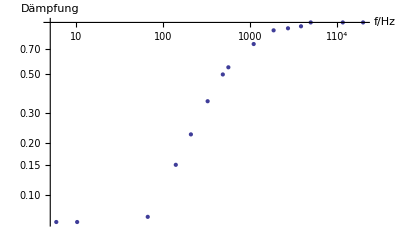

```mathematica
Show[ ListLogLogPlot[phD,AxesOrigin->{5,1}],AxesLabel->{"f/Hz","Dämpfung"}]
```

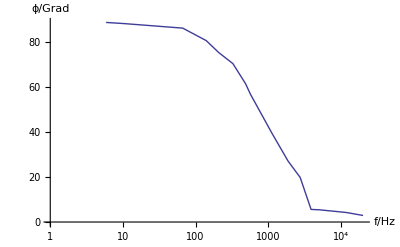

```mathematica
Show[ ListLogLinearPlot[phϕ,Joined->True,AxesOrigin->{0,0}],AxesLabel->{"f/Hz","ϕ/Grad"}]
```

## 2.) Tiefpass

```mathematica
tpt =
{{15, 0, 4}, {57.27, 0.2, 4}, {105.9, 0.2, 4}, {266.8, 0.2, 3.8}, {402.5, 0.2, 3.6}, {565.2, 0.16, 3.3}, {1052, 0.130, 2.5}, {2144, 0.090, 2}, {3543, 0.06, 0.9}, {4760, 0.048, 0.7}, {5311, 0.044, 0.6}, {5760, 0.040, 0.56}, {10460, 0.022, 0.32}, {19610, 0.012, 0.16}};
```

```mathematica
tpϕ = Table[{tpt[[x,1]]*tpt[[x,2]]*10^-3*360},{x,1,14}];
tpD = Table[{tpt[[x,3]]/Ue},{x,1,14}];
```

```mathematica
ptD = Table[{tpt[[x,1]],tpD[[x,1]]},{x,1,Length[tpD]}];
ptϕ = Table[{tpt[[x,1]],tpϕ[[x,1]]},{x,1,Length[tpD]}];
```

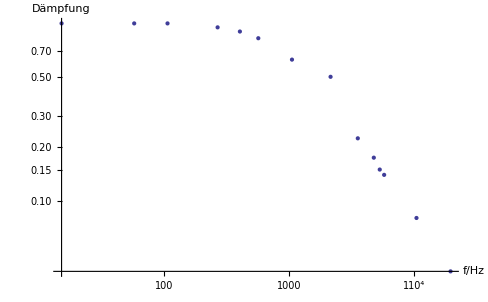

```mathematica
Show[ ListLogLogPlot[ptD],AxesLabel->{"f/Hz","Dämpfung"}]
```

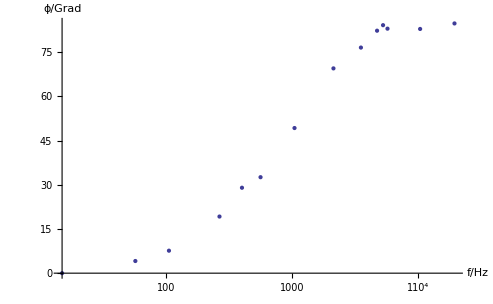

```mathematica
Show[ ListLogLinearPlot[ptϕ(*,AxesOrigin->{0,0}*)],AxesLabel->{"f/Hz","ϕ/Grad"}]
```

{22462,1}

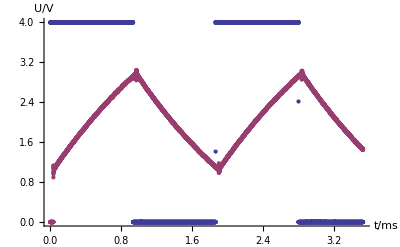

```mathematica
int=Import["/home/michael/tug/labor/2/int_htp.dso","Table"];
Dimensions[int]
pdata=Table[{x*2/5674,int[[x,1]]/255*4},{x,1,10000}];
pdata2=Table[{(x-10000)*2/5674,int[[x,1]]/255*4},{x,10001,20000}];
ListPlot[{pdata,pdata2},AxesLabel->{"t/ms","U/V"}]
```

```mathematica
2/(1800*2/(0.9 10^-3))//N
```

5.×10^-7

{22462,1}

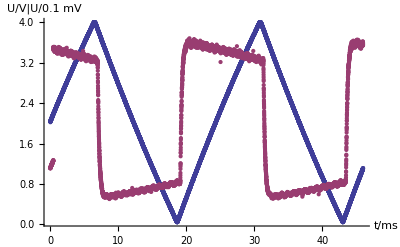

```mathematica
int2=Import["/home/michael/tug/labor/2/dif_htp.dso","Table"];
Dimensions[int2]
pddata=Table[{x*2/(47.18*9.215),int2[[x,1]]/255*4},{x,1,10000}];
pddata2=Table[{(x-10000)*2/(9.215*47.18),int2[[x,1]]/255*4},{x,10001,20000}];
ListPlot[{pddata,pddata2},AxesLabel->{"t/ms","U/V|U/0.1 mV"}]
```

```mathematica
((3.4-0.7)*10^-4)/(2 1800)*10.5/4*10^6
```

0.196875